# Distinct Graphs with Similar Stats

Generating datasets which are visually different while sharing the same statistical properties

Tanha Kate, Jun. 29,  2018

## Background

Anscombe’s Quartet is a set of four different-looking datasets with the same summary statistics (mean, standard deviation, and correlation). The Quartet is popular in introductory statistics courses to illustrate the importance of visualizing data.

```mathematica
Import["http://www.lac.inpe.br/~rafael.santos/Docs/R/CAP386/figure/viz_ggplot_basescatter1-1.png"]
```

-Graphics-

Developed in 1973, it is still unknown how Anscombe came up with his datasets.

Recently, Matejka et al. (2017) developed a novel technique to generate visually different datasets which share the same summary statistics. We will implement their technique on Mathematica using a dinosaur-shaped dataset, titled the Datasaurus , which was used originally in Matejka et al.'s paper.

## Steps

The key component of Matejka et al.’s algorithm is that its relatively easy to take an existing dataset and modify it slightly, while preserving statistical properties. With repetition, the process produces very different graphs, and the shape of these graphs can be directed towards a particular target shape.

At first, we will import and visualize the Datasaurus dataset (Cairo, n.d.). Datasaurus is a list containing pairs of coordinates in the shape of a dinosaur.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
dataset = Import["Datasaurus_data.csv","CSV"]
```

{{55.3846,97.1795},{51.5385,96.0256},{46.1538,94.4872},{42.8205,91.4103},{40.7692,88.3333},{38.7179,84.8718},{35.641,79.8718},{33.0769,77.5641},{28.9744,74.4872},{26.1538,71.4103},{23.0769,66.4103},{22.3077,61.7949},{22.3077,57.1795},{23.3333,52.9487},{25.8974,51.0256},{29.4872,51.0256},{32.8205,51.0256},{35.3846,51.4103},{40.2564,51.4103},{44.1026,52.9487},{46.6667,54.1026},{50,55.2564},{53.0769,55.641},{56.6667,56.0256},{59.2308,57.9487},{61.2821,62.1795},{61.5385,66.4103},{61.7949,69.1026},{57.4359,55.2564},{54.8718,49.8718},{52.5641,46.0256},{48.2051,38.3333},{49.4872,42.1795},{51.0256,44.1026},{45.3846,36.4103},{42.8205,32.5641},{38.7179,31.4103},{35.1282,30.2564},{32.5641,32.1795},{30,36.7949},{33.5897,41.4103},{36.6667,45.641},{38.2051,49.1026},{29.7436,36.0256},{29.7436,32.1795},{30,29.1026},{32.0513,26.7949},{35.8974,25.2564},{41.0256,25.2564},{44.1026,25.641},{47.1795,28.718},{49.4872,31.4103},{51.5385,34.8718},{53.5897,37.5641},{55.1282,40.641},{56.6667,42.1795},{59.2308,44.4872},{62.3077,46.0256},{64.8718,46.7949},{67.9487,47.9487},{70.5128,53.718},{71.5385,60.641},{71.5385,64.4872},{69.4872,69.4872},{46.9231,79.8718},{48.2051,84.1026},{50,85.2564},{53.0769,85.2564},{55.3846,86.0256},{56.6667,86.0256},{56.1538,82.9487},{53.8462,80.641},{51.2821,78.718},{50,78.718},{47.9487,77.5641},{29.7436,59.8718},{29.7436,62.1795},{31.2821,62.5641},{57.9487,99.4872},{61.7949,99.1026},{64.8718,97.5641},{68.4615,94.1026},{70.7692,91.0256},{72.0513,86.4103},{73.8462,83.3333},{75.1282,79.1026},{76.6667,75.2564},{77.6923,71.4103},{79.7436,66.7949},{81.7949,60.2564},{83.3333,55.2564},{85.1282,51.4103},{86.4103,47.5641},{87.9487,46.0256},{89.4872,42.5641},{93.3333,39.8718},{95.3846,36.7949},{98.2051,33.718},{56.6667,40.641},{59.2308,38.3333},{60.7692,33.718},{63.0769,29.1026},{64.1026,25.2564},{64.359,24.1026},{74.359,22.9487},{71.2821,22.9487},{67.9487,22.1795},{65.8974,20.2564},{63.0769,19.1026},{61.2821,19.1026},{58.7179,18.3333},{55.1282,18.3333},{52.3077,18.3333},{49.7436,17.5641},{47.4359,16.0256},{44.8718,13.718},{48.7179,14.8718},{51.2821,14.8718},{54.1026,14.8718},{56.1538,14.1026},{52.0513,12.5641},{48.7179,11.0256},{47.1795,9.8718},{46.1538,6.0256},{50.5128,9.4872},{53.8462,10.2564},{57.4359,10.2564},{60,10.641},{64.1026,10.641},{66.9231,10.641},{71.2821,10.641},{74.359,10.641},{78.2051,10.641},{67.9487,8.718},{68.4615,5.2564},{68.2051,2.9487},{37.6923,25.7692},{39.4872,25.3846},{91.2821,41.5385},{50,95.7692},{47.9487,95},{44.1026,92.6923}}

```mathematica
ListPlot[dataset]
```

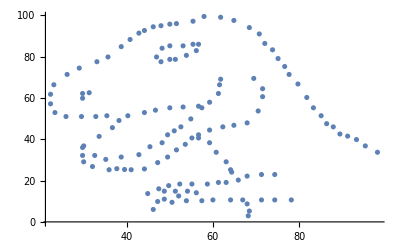

```mathematica
ListPlot[dataset]
```

Our next step is to define a function to generate the descriptive statistics for Datasaurus.

```mathematica
summaryStatistics[data_]:={Mean[data],StandardDeviation[data],Correlation[data]⟦1,2⟧}
```

```mathematica
summaryStatistics[dataset]
```

{{54.2633,47.8323},{16.7651,26.9354},-0.0644719}

Then, we will select a target shape that we want Datasaurus to conform to. In this notebook, we will proceed with a circle centered at {54.26,47.83}, with a radius of 30.

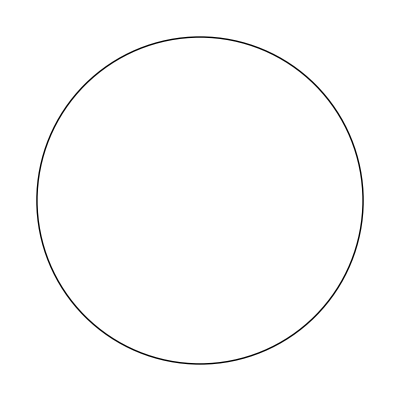

```mathematica
Graphics[Circle[{54.26,47.83},30]]
```

At this stage, we want to move individual coordinates by a small amount  chosen from a normal distribution. Hence, we will define the moveRandomPoint function to complete a single round of such a perturbation.

```mathematica
moveRandomPoint[{x_,y_}]:={x,y}+RandomVariate[NormalDistribution[0,1],2];
```

```mathematica
newDataset=Map[moveRandomPoint,dataset];
```

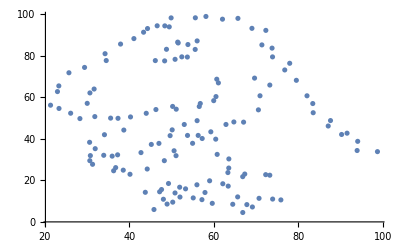

```mathematica
ListPlot@newDataset
```

The data-points look slightly shifted, but we still need a way to approximate towards our target shape. To accomplish this task, we will define functionFit, which  computes the average minimum distance between the coordinates in our dataset and our target shape, i.e. a circle using the built-in RegionDistance.

```mathematica
functionFit1[{x_,y_}]:=List[RegionDistance[Circle[{54.26,47.83},30],{x,y}]];
functionFit[list_]:=First[Mean[functionFit1/@list]]
```

The final step in our algorithm is to check whether the previous dataset and the new dataset are statistically equivalent (within 2 decimal places), using an isErrorokay function.

```mathematica
isErrorokay[data1_,data2_]:=If[Abs[Total[Flatten[summaryStatistics[data1]-summaryStatistics[data2]]]]<1,True,False]
```

```mathematica
isErrorokay[dataset,newDataset]
```

True

To put it all together, as long as the newly generated dataset has a higher fitness score (i.e. the coordinates are, on average, closer to our target shape), and if it is statistically equivalent to our original dataset, we will repeat the process of perturbing our data for a specified number of iterations using a Nest function.

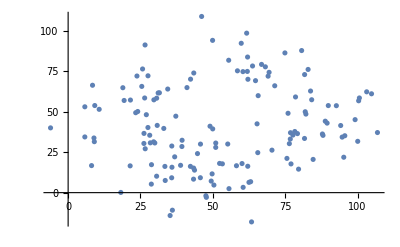

```mathematica
ListPlot@Nest[Catch[Do[With[{newDataset=Map[moveRandomPoint,#]},
If[functionFit[newDataset]< functionFit[dataset]&& isErrorokay[dataset,newDataset],Throw[newDataset]]],{i,100}]]&,dataset,5000]
```

With 5000 iterations, the dinosaur has completely disappeared from our graph, and a hollow, circular region is emerging in the center, yet both our Datasaurus and the perturbed dataset share the same mean, standard deviation and Pearson’s correlation.

## Final Remarks

At present, our algorithm implements the naive approach which accepts datasets only with an improved fitness value. To mitigate the possibility of early convergence in locally-optimal solutions, Matejka et al. suggests a simulated annealing technique, which accepts solutions based on a “temperature” measure even if the fitness isn’t improved. You can find out more about their technique in the paper referenced in the section below.

As a concluding remark, don’t trust numbers that describe your dataset until you’ve seen the shape of the data for yourself.

## Further explorations

Anscombe, F.J. (1973). Graphs in Statistical Analysis. The American Statistician 27, 1, 17–21.

Cairo, A. (n.d.). Download the Datasaurus: Never trust summary statistics alone; always visualize your data. Retrieved June 29, 2018, from http://www.thefunctionalart.com/2016/08/download-datasaurus-never-trust-summary.html

Matejka, J., & Fitzmaurice, G. (2017). Same Stats, Different Graphs: Generating Datasets with Varied Appearance and Identical Statistics Through Simulated Annealing. In Proceedings of the 2017 CHI Conference on Human Factors in Computing Systems (pp. 1290–1294). New York, NY, USA: ACM. https://doi.org/10.1145/3025453.3025912

## Author contact information

tanha.kate@minerva.kgi.edu